## 2/5/19 lab section

```mathematica
(*midterm review*)

(*
1) Calculate the sine of the golden angle (with a calculator-like output).
*)

Sin[GoldenAngle]//N
```

0.67549

```mathematica
(*
2. Create a list of five objects and randomly choose one of them.Then replace the third object in
the list with a new object.Check the new list.
*)
```

```mathematica
list={1,2,3,4,};
choice=RandomChoice[list]
list[[3]]="new object";
list
```

4

{1,2,new object,4,Null}

```mathematica
(*
3. Automatically create nine fractions in the form 1/2,1/3,1/4,…,1/10. Automatically calculate the
sum of the list (as a decimal approximation).
*)
a=Range[2,10];
f[x_]:=1/x
b=f/@a
Total[b]//N
```

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

1.92897

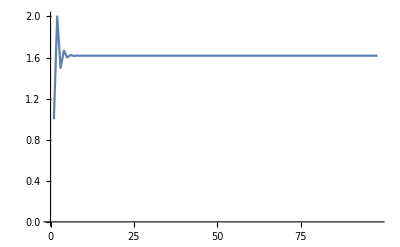

```mathematica
(*
4. Use the previous problem as an example.Create 100 ratios of Fibonacci numbers,such that
each ratio is a Fibonacci number divided by its neighbor on the left (starting with the second Fibonacci number).Since the Fibonacci sequence is (1,1,2,3,...),the required sequence should
be (1/1,2/1,3/2,…).Plot the list.The sequence should approach a definite limit (which happens to be the golden ratio or 1.6…).
*)
size=100;
a=Fibonacci[Range[size]];
b=Table[1,size-2,0];
For[i=1,i<size-1,b[[i-1]]=a[[i]]/a[[i-1]],i++];
ListLinePlot[b]
```

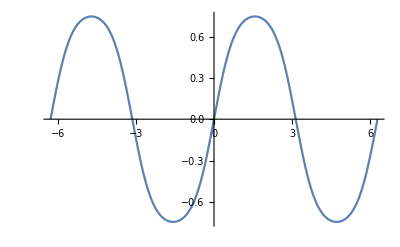

```mathematica
(*
5. Plot the function that is the sine of the sine of the sine of x,where x ranges from-2π to 2π.
*)
Plot[Sin[Sin[Sin[x]]],{x,-2Pi,2Pi}]
```

```mathematica
(*
6. Find if you were born in a prime year.
*)
PrimeQ[1996]
```

False

```mathematica
(*
7. Create a loop that prints the squares of the first 10 natural numbers (1,2,3,…).
*)
For[i=1,i≤10,i++,Print[i^2]]
```

1

4

9

16

25

36

49

64

81

100

```mathematica
(*
8. Create a list of your five friends.Use a loop to produce automatic greetings for each one of
them.For example,if the initial list is (Joe,Jane,…),the output should be (“Hi Joe!”,“Hi Jane!”,…).
*)
```

```mathematica
x={"erick1","erick2","erick3","erick4","erick5"};
For[i=1,i≤5,i++,Print["hi ",x[[i]],"!"]]
```

hi erick1!

hi erick2!

hi erick3!

hi erick4!

hi erick5!

```mathematica
(*
9. Run the command Pi=3.14.Explain its result.Now run the command Pi==3.14.Explain this new result
*)
Pi=3.14
```

Set::wrsym: Symbol π is Protected.

3.14

```mathematica
(*this is because you're trying to assign the value 3.14 to Pi, which already has a value and is proctected*)
```

```mathematica
Pi==3.14
```

False

```mathematica
(*this is a logical statement, so it tell you that Pi is not equal to 3.14*)
```

```mathematica
(*
10. Run the following command:RegionPlot3D[True,{x,0,1},{y,0,1},{z,0,1},AxesLabel->{x,y,z},RotationAction->"Clip"]
Now try:RegionPlot3D[x>0.5,{x,0,1},{y,0,1},{z,0,1},AxesLabel->{x,y,z},RotationAction->"Clip"].What does the function do?“Sculpt” with various logical conditions on x,y,and z (==, >, &&, ||,etc.).
*)


RegionPlot3D[True,{x,0,1},{y,0,1},{z,0,1},AxesLabel->{x,y,z},RotationAction->"Clip"]
```

-Graphics3D-

```mathematica
Clear[x]
RegionPlot3D[x>0.8,{x,0,1},{y,0,1},{z,0,1},AxesLabel->{x,y,z},RotationAction->"Clip"]
```

-Graphics3D-